Optimization utilities.

Original opt_inverse is contained in $IGHOME/inverse.

Many definitions were taken from that notebook.

This notebook contains initialization cells that are used to set up the necessary definitions.

Set working directory:
   Allways check that  working directory is set correctly!

```mathematica
(* Gradbena:
SetDirectory["E:/users/c3m/igor/enlub/work/SRT_identification_2006-01-20/StripReduction"]
*)

SetDirectory["c:/users/igor/doc/pr/enlub/work/SRT_identification_2006-01-20/StripReduction/"]
```

c:\users\igor\doc\pr\enlub\work\SRT_identification_2006-01-20\StripReduction

Running optimization from "Inverse"  - debugging mode

### Instructions: For debugging, run Inverse from debugger with the -linkcreate option, e.g. C:/users/igor/cz/invmath.exe optmath.cm -linkcreate A message box is launched stating the name of the link. You must insert this name in the cell below and evaluate it, then swithch to debugger and perform debugging (don't forget to set breakpoints).

### Important note: Correct directory paths before evaluation!

```mathematica
(* For debugging - insert the reported link name (copy from message box) first! *)
link=Install[LinkConnect["bmr_shm"]];
InvInterpret[]
```

{KONTROLA: InvInterpret - finished.}

## Run "Inverse" - test This will run "Inverse". (This is a test, otherwise Inverse is run by the command runinverse[]. )

You don't need to run this if you don't do optimization with Inverse.

### Checks for of runiverse[ ]

#### Important note: Correct directory paths before evaluation!

```mathematica
(*
SetDirectory["C:\\users\\igor\\c\\0exmath"];
link=Install["C:\users\igor\cz\invmath.exe invmath.cm"];
*)

(* Remark: command file default.cm must be in the current directory before evaluating this cell. The file can be empty.  *)
link=Install["invmath.exe default.cm"];

Print["Running ",InvGetVar["string","program",{}]," ",InvGetVar["scalar","version",{}],"."]

InvInterpret[]

runinverse[]
```

Running Inverse 3.12.

{KONTROLA: InvInterpret - finished.}

```mathematica
Directory[]
```

c:\users\igor\doc\pr\enlub\work\SRT_identification_2006-01-20\StripReduction

# Collection of Graphical Utilities for Optimization

```mathematica
If[testmode≠0,testmode=0;];
If[debugmode≠0,debugmode=0;];
```

## Plots of algorithm progress

### plotalgpath

```mathematica
plotalgpath[taban_,def_,pointsize_,thickness_,color_,graphlabels_,showplot_]:=Module[{tabparam,tabpoints,i,j,choice,tabchoice,ret,gr,labels},choice=N[def];labels=Table["Parameter "<>ToString[choice⟦i⟧],{i,1,Length[def]}];If[Depth[choice]>2,Return[Table[plotalgpath[taban,def⟦i⟧,pointsize,thickness,color,graphlabels,showplot],{i,1,Length[choice]}]];];tabparam=Table[anptparam[taban⟦i⟧],{i,1,Length[taban]}];tabpoints=Table[Table[tabparam⟦i,choice⟦j⟧⟧,{j,1,Length[choice]}],{i,1,Length[tabparam]}];gr=pointsgraph[tabpoints,pointsize,thickness,color];If[showplot≠0,Print["Algorithm path with respect to parameters ",choice,": "];If[Length[choice]==2,Show[gr,Axes->True,Frame->True,FrameLabel->labels,PlotRange->All,AspectRatio->1],Show[gr,Axes->True,FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},AxesLabel->labels,BoxRatios->{1,1,1},PlotRange->All,ViewPoint->{3.892,-7.185,3.771}]];];Return[gr];];
```

### Tests of algorithm progress plots:

#### Analysis history test data (var. testanhistory), copied from SQP on strip reduction example):

```mathematica
If[testmode≠0,

testanhistory={{{45.,100.,6.},{1,12061.,0,{},1,{90.,200.,12.},0,{},-1},{1,1,1,1,"3"}},{{45.,100.,6.},{1,12061.,0,{},1,{90.,200.,12.},0,{},-1},{1,1,1,1,"3"}},{{45.,100.,6.},{1,12061.,0,{},1,{90.,200.,12.},0,{},-4},{1,1,1,1,""}},{{45.,100.,6.},{1,591.0716545075418,0,{},1,{-45.29186153322917,0.13466170848014997,3.6554809271472055},0,{},-1},{1,1,1,1,"1"}},{{90.29186153322917,99.86533829151985,2.3445190728527945},{1,961.8920869730232,0,{},1,{58.663146918671856,-4.591422836159392,-116.60852955181826},0,{},-1},{1,1,1,1,"1"}},{{67.64593076661458,99.93266914575993,4.172259536426397},{1,145.35260970931262,0,{},1,{5.545131312785147,-1.2448499166512192,-23.11436994039195},0,{},-1},{1,1,1,1,"1"}},{{74.35244058138785,100.96925732911485,23.12695429270905},{1,84.19362189981821,0,{},1,{9.996531668571691,-0.43216393072689024,-0.9967433542333446},0,{},-1},{1,1,1,1,"1"}},{{69.37445660600575,101.24971881897699,21.961828230101972},{1,61.51592420907083,0,{},1,{0.22266135526379857,-0.26149112570640937,-0.30030646071308975},0,{},-1},{1,1,1,1,"1"}},{{69.30847479174986,101.5153440349123,22.165170801483757},{1,61.381965939153126,0,{},1,{0.04571827082790243,-0.25335604525387695,-0.25789541310027775},0,{},-1},{1,1,1,1,"1"}},{{69.27670516494341,103.30135069646438,23.556671303059026},{1,60.74884049657558,0,{},1,{-0.3005060409017983,-0.21639975996747,-0.0627699255059139},0,{},-1},{1,1,1,1,"1"}},{{69.47459094445881,106.28045677332413,25.72299518961667},{1,59.57585553949494,0,{},1,{-0.3714211901233956,-0.17309951428248677,0.14214792919169375},0,{},-1},{1,1,1,1,"1"}},{{69.68509706997979,108.06549038895265,26.791120813504197},{1,58.689422426583114,0,{},1,{-0.16451482374495985,-0.15962034981752757,0.20908944696888426},0,{},-1},{1,1,1,1,"1"}},{{69.8386704893342,109.6680753768298,27.43120859369262},{1,58.088850192247754,0,{},1,{0.34154055473786454,-0.1520973654153092,0.22022765787191123},0,{},-1},{1,1,1,1,"1"}},{{69.87942816861693,112.5196746807235,28.172278338143855},{1,57.88342874071873,0,{},1,{0.25981235177803247,-0.13356467077510611,0.2886075600789327},0,{},-1},{1,1,1,1,"1"}},{{69.88769987279329,118.87109110147759,28.74806759922201},{1,57.3175415083021,0,{},1,{0.05588488881945822,-0.10648811454824124,0.3761697566457032},0,{},-1},{1,1,1,1,"1"}},{{69.82265359677702,136.39219132438947,28.42393014460885},{1,57.0771404569637,0,{},1,{-0.6895087136539283,-0.06260779040485336,0.5309861795004981},0,{},-1},{1,1,1,1,"1"}},{{69.78931883077527,175.553772963308,25.07124634622802},{1,51.87367627437132,0,{},1,{-0.5849970173595822,-0.037307891404471556,0.5805893175477659},0,{},-1},{1,1,1,1,"1"}},{{69.25124703832174,344.0271868935814,6.504441128598398},{1,54.370494864700895,0,{},1,{0.7787213725215456,-0.050317234686259364,-4.604975865488677},0,{},-1},{1,1,1,1,"1"}},{{69.5202829345485,259.7904799284447,15.787843737413208},{1,45.209199850282644,0,{},1,{-0.5807746391753256,-0.03053722678213401,0.15323924312689316},0,{},-1},{1,1,1,1,"1"}},{{69.50898155694874,343.4903774349846,8.13128353669535},{1,48.845253173828894,0,{},1,{0.5215827365926504,-0.04013089599192758,-2.6072735498845336},0,{},-1},{1,1,1,1,"1"}},{{69.51463224574861,301.64042868171464,11.959563637054279},{1,44.515264189481044,0,{},1,{-0.025497697810151012,-0.03352249173992602,-0.599166304606414},0,{},-1},{1,1,1,1,"1"}},{{69.7230826616893,307.11962727501106,13.275870795745638},{1,43.823252642239936,0,{},1,{0.04126197888871293,-0.027488913243049286,-0.22129128194460015},0,{},-1},{1,1,1,1,"1"}},{{70.10835949295748,347.7522515013816,13.705701672227713},{1,43.455686045811184,0,{},1,{0.23094894605613128,-0.019047691536016344,-0.040700976381906645},0,{},-1},{1,1,1,1,"1"}},{{70.63043945485748,425.5538671436991,13.410561241326212},{1,42.039519485727254,0,{},1,{0.8026659120184955,-0.012362663431131514,-0.022103853565648472},0,{},-1},{1,1,1,1,"1"}},{{70.82556453309631,490.68103746277325,12.836406688454165},{1,43.283227148000705,0,{},1,{1.4432487206650635,-0.009789552179621146,-0.12442613216709719},0,{},-1},{1,1,1,1,"1"}},{{70.7280019939769,458.1174523032362,13.123483964890188},{1,43.74574611564184,0,{},1,{1.158510636794328,-0.010698795418658423,-0.049387822583386976},0,{},-1},{1,1,1,1,"1"}},{{70.67922072441719,441.83565972346764,13.2670226031082},{1,43.67737612739491,0,{},1,{1.0528047935358247,-0.011438279381810641,-0.028707409092736565},0,{},-1},{1,1,1,1,"1"}},{{70.65483008963733,433.6947634335834,13.338791922217206},{1,41.96260758820653,0,{},1,{0.8435465980942795,-0.011913556770955456,-0.02837487256474725},0,{},-1},{1,1,1,1,"1"}},{{70.76990574163277,570.7769748438379,12.046012854049115},{1,42.67533330805756,0,{},1,{1.4035751489460768,-0.007296538654080216,-0.22917725534685973},0,{},-1},{1,1,1,1,"1"}},{{70.71236791563506,502.23586913871065,12.69240238813316},{1,43.13612439098826,0,{},1,{1.1033413481168128,-0.008847694378785213,-0.0797207292413703},0,{},-1},{1,1,1,1,"1"}},{{70.68359900263619,467.965316286147,13.015597155175184},{1,43.4097415123633,0,{},1,{1.0513682066641594,-0.01014577245808726,-0.04517274771613451},0,{},-1},{1,1,1,1,"1"}},{{70.66921454613676,450.8300398598652,13.177194538696195},{1,41.7841846368067,0,{},1,{0.8618430851967607,-0.01099306598632651,-0.038716389657617485},0,{},-1},{1,1,1,1,"1"}},{{70.60494207684324,619.3581877762604,11.65295336905391},{1,42.240904753047836,0,{},1,{1.1063637665833237,-0.006058086800821434,-0.25806556630876093},0,{},-1},{1,1,1,1,"1"}},{{70.63707831149,535.0941138180629,12.415073953875051},{1,41.03404042130823,0,{},1,{0.7867259947691485,-0.007689956753999533,-0.09847155575579168},0,{},-1},{1,1,1,1,"1"}},{{70.47969160794055,693.8378166902387,11.376635297564063},{1,41.79611955581985,0,{},1,{0.8406979324800219,-0.00458053973575583,-0.246640627675779},0,{},-1},{1,1,1,1,"1"}},{{70.55838495971527,614.4659652541508,11.895854625719556},{1,42.16912854720596,0,{},1,{0.9672987517207741,-0.005860289157734275,-0.17641419572600348},0,{},-1},{1,1,1,1,"1"}},{{70.59773163560264,574.7800395361069,12.155464289797305},{1,42.41579639229132,0,{},1,{1.0416089659715835,-0.006763621691184038,-0.15303157089921793},0,{},-1},{1,1,1,1,"1"}},{{70.61740497354631,554.9370766770849,12.285269121836178},{1,40.88568606635733,0,{},1,{0.7428062268016188,-0.0070843241887289105,-0.10427951763702477},0,{},-1},{1,1,1,1,"1"}},{{70.38457839231936,762.6076685016334,11.311827517659978},{1,41.426954313735834,0,{},1,{0.6016812607463776,-0.0035286798486598918,-0.19104427465409374},0,{},-1},{1,1,1,1,"1"}},{{70.50099168293283,658.7723725893591,11.798548319748077},{1,41.896581761194554,0,{},1,{0.8231126586814826,-0.004878798774576684,-0.14872774196269176},0,{},-1},{1,1,1,1,"1"}},{{70.55919832823957,606.854724633222,12.041908720792128},{1,42.191498293111344,0,{},1,{0.9462851856216871,-0.005903081759870337,-0.14116192028110408},0,{},-1},{1,1,1,1,"1"}},{{70.58830165089294,580.8959006551535,12.163588921314153},{1,42.36421489129626,0,{},1,{1.0123878890185454,-0.0065479209196187445,-0.1413442031099209},0,{},-1},{1,1,1,1,"1"}},{{70.60285331221962,567.9164886661191,12.224429021575165},{1,42.45788293982713,0,{},1,{1.0467573234079792,-0.006912115158547468,-0.14253327079408049},0,{},-1},{1,1,1,1,"1"}},{{70.61012914288297,561.426782671602,12.254849071705673},{1,42.506696069211685,0,{},1,{1.0642926989777381,-0.007106000949714414,-0.14341839209610832},0,{},-1},{1,1,1,1,"1"}},{{70.61376705821465,558.1819296743435,12.270059096770925},{1,40.861756513862645,0,{},1,{0.7337126246027057,-0.0069845859664727315,-0.1036633873070098},0,{},-1},{1,1,1,1,"1"}},{{69.88005443361195,558.18891426031,12.373722484077936},{1,40.601959431508604,0,{},1,{-0.18201773319161046,-0.005925118727608888,0.05140106725079289},0,{},-1},{1,1,1,1,"1"}},{{70.0247388702146,558.1936493726356,12.332779388494759},{1,41.116693075128325,0,{},1,{-0.22711479028554998,-0.005973160071503125,0.027872426756260723},0,{},-1},{1,1,1,1,"1"}},{{69.95239665191328,558.1912818164727,12.353250936286347},{1,41.4654749160951,0,{},1,{-0.4586219836486747,-0.005595878187770747,0.06843717502999724},0,{},-1},{1,1,1,1,"1"}},{{69.9162255427626,558.1900980383914,12.363486710182142},{1,40.596207341287574,0,{},1,{-0.10951246008453844,-0.005995034750967309,0.04096230997908652},0,{},-1},{1,1,1,1,"1"}},{{69.97074279536596,558.1982508232246,12.321781879720515},{1,42.28402387384724,0,{},1,{-0.37712961894611097,-0.005678525563014271,0.06131844043054342},0,{},-1},{1,1,1,1,"1"}},{{69.94348416906429,558.194174430808,12.342634294951328},{1,40.5932321074614,0,{},1,{-0.05201767162799964,-0.006063470948086752,0.02964619906049088},0,{},-1},{1,1,1,1,"1"}},{{69.9707456490624,558.2053862921921,12.298960590529791},{1,42.28265051559714,0,{},1,{-0.37221159343192256,-0.00570553767386572,0.05538031313788702},0,{},-1},{1,1,1,1,"1"}},{{69.95711490906334,558.1997803615,12.32079744274056},{1,41.461233151626516,0,{},1,{-0.44231977111226417,-0.0056417781895590335,0.059028723826460766},0,{},-1},{1,1,1,1,"1"}},{{69.95029953906382,558.196977396154,12.331715868845944},{1,41.46498549634762,0,{},1,{-0.4581744753853359,-0.005618012492325061,0.06332455797331606},0,{},-1},{1,1,1,1,"1"}},{{69.94689185406405,558.195575913481,12.337175081898636},{1,41.46691973704941,0,{},1,{-0.46610162739246824,-0.005606140553331199,0.06546808321817901},0,{},-1},{1,1,1,1,"1"}},{{69.94518801156417,558.1948751721444,12.339904688424982},{1,40.59306310117443,0,{},1,{-0.048120440778124524,-0.006069453100273124,0.0285638741616029},0,{},-1},{1,1,1,1,"1"}},{{69.9701598239189,558.2138213852323,12.277997836028199},{1,42.28171451827403,0,{},1,{-0.36886759510948,-0.005729410297833706,0.05002489015172508},0,{},-1},{1,1,1,1,"1"}},{{69.95767391774154,558.2043482786884,12.308951262226591},{1,41.46028081597015,0,{},1,{-0.43860563775024475,-0.005656734607653196,0.05582771527846543},0,{},-1},{1,1,1,1,"1"}},{{69.95143096465286,558.1996117254164,12.324427975325786},{1,41.464000705416936,0,{},1,{-0.4543703957132028,-0.005628421018761309,0.061193375643342054},0,{},-1},{1,1,1,1,"1"}},{{69.9483094881085,558.1972434487803,12.332166331875383},{1,40.59269998256107,0,{},1,{-0.04038966801113517,-0.00608367508280314,0.025861857193001343},0,{},-1},{1,1,1,1,"1"}},{{69.96827880378774,558.2220856462556,12.26311178317268},{1,42.28164279752714,0,{},1,{-0.3694045060208364,-0.005743965276386955,0.046526069647822466},0,{},-1},{1,1,1,1,"1"}},{{69.95829414594813,558.209664547518,12.297639057524032},{1,41.45936570195518,0,{},1,{-0.4349487632794651,-0.005671097977444403,0.05274406119373849},0,{},-1},{1,1,1,1,"1"}},{{69.95330181702832,558.2034539981491,12.314902694699708},{1,41.46256517523878,0,{},1,{-0.44861963933671767,-0.005642649709818045,0.058318182249956975},0,{},-1},{1,1,1,1,"1"}},{{69.9508056525684,558.2003487234648,12.323534513287546},{1,41.46422637798076,0,{},1,{-0.4554197641676842,-0.00562847184563935,0.06109642372561655},0,{},-1},{1,1,1,1,"1"}},{{69.94955757033846,558.1987960861226,12.327850422581465},{1,41.46507231416001,0,{},1,{-0.45881922694686494,-0.005621388169180855,0.06248328819054527},0,{},-1},{1,1,1,1,"1"}},{{69.94893352922348,558.1980197674515,12.330008377228424},{1,41.4654991129182,0,{},1,{-0.4605188086112428,-0.005617847643622857,0.06317615720211361},0,{},-1},{1,1,1,1,"1"}},{{69.948621508666,558.1976316081159,12.331087354551903},{1,40.592657433947636,0,{},1,{-0.039550957363224275,-0.006085460039731679,0.025511436763086093},0,{},-1},{1,1,1,1,"1"}},{{69.96635959375536,558.2301104756813,12.252867160037805},{1,41.453784741684004,0,{},1,{-0.4093156096536921,-0.005737098763173482,0.03923617327606394},0,{},-1},{1,1,1,1,"1"}},{{69.95749055121068,558.2138710418986,12.291977257294853},{1,41.459396576612654,0,{},1,{-0.4353285944945471,-0.005676476363475742,0.05143936900237617},0,{},-1},{1,1,1,1,"1"}},{{69.95305602993834,558.2057513250072,12.311532305923379},{1,41.46246727548174,0,{},1,{-0.4483859195111123,-0.005646217670656781,0.05749554877418472},0,{},-1},{1,1,1,1,"1"}}}  ;

,,]
```

```mathematica
Length[anhistory]
```

0

```mathematica
If[testmode≠0,
testantab=Take[testanhistory,{ 1,-1,1 (* step *)}];
,,]
```

```mathematica
If[testmode≠0,
(* A single plot: *)
testplot=plotalgpath[testantab,{1,2},0.02,0.005,{1,0.2,0},{},1]
,,]
```

```mathematica
If[testmode≠0,

(* Creating multiple plots by a single command by passing a list of selection lists instead of a singe selection list: *)
{testplot,testplot1,testplot2,testplot3}=testtabplot=plotalgpath[testantab,
{
{1,2,3},
{1,2},
{1,3},
{2,3}
},
0.02,0.005,{1,0.2,0},{},1];

,,]
```

## Plotting tables of points & grids

### handlecolor [ col ] converts col to a valid color. col a valid color specification such as Hue[0.5] or RGBColor[1,0,0.5]: col is returned. col an integer greater than or equal to 1 - a color is picked from a global palette (index overflow is handled internally). col a number between 0 and 1 - Hue[col] is returned col a list of three numbers - RGBColor[ col[[1]], col[[2]], col[[3]] ] is returned. rgbpalette [ numshades ] creates a palette of RGB colors with numshades shades for each basic color. testcolors [ cols ] plots all colors in the color list cols (which can be arbitrarily structured because the list is flattened)

```mathematica
(testcolors[cols_]:=testcolors0[Flatten[cols]];) (testcolors0[cols_]:=Show[Graphics[Table[{Thickness[0.5/Length[cols]],cols⟦i⟧,Line[{{0,i/Length[cols]},{1,i/Length[cols]}}]},{i,1,Length[cols]}]],PlotRange->All]) (rgbcolorpalette[numshades_]:=Flatten[Table[Table[Table[N[RGBColor[i/(numshades+0.5),j/(numshades+0.5),k/(numshades+0.5)]],{k,0,numshades-1}],{j,0,numshades-1}],{i,0,numshades-1}]];) (handlecolor[color_]:=Block[{col,palette={},minpalette=8},palette=colors;col=color;If[VectorQ[col,NumberQ]&&Length[col]==3,Return[RGBColor[col⟦1⟧,col⟦2⟧,col⟦3⟧]];];If[ListQ[col],If[Length[col]==0,Return[RGBColor[0,0,0]]];Return[handlecolor[color⟦1⟧]];];If[IntegerQ[col],If[col<1,Return[RGBColor[0,0,0]]];If[col>200,col=Mod[col,200]];If[Length[palette]<minpalette||Length[palette]<col,If[Length[palette]<minpalette,palette=Table[Hue[N[i/minpalette]],{i,0,minpalette-1}];];While[Length[palette]<col,palette=Join[palette,palette]];maincolorpalette=palette;];col=palette⟦col⟧;Return[col];];If[NumberQ[col],If[col<0,col=0];If[col>1,col=1];col=Hue[col];];If[Depth[col]<2,Return[RGBColor[0,0,0]];];Return[col];];) (rgbcolorpalette0[numshades_]:=Module[{ret,ind={0,0,0},whichshade=1,indtab},indtab=Sort[Flatten[Table[Table[Table[{i,j,k},{k,0,numshades-1}],{j,0,numshades-1}],{i,0,numshades-1}],2],Module[{sum1,sum2,ret},sum1=∑_(i=1)^Length[#1] #1⟦i⟧;sum2=∑_(i=1)^Length[#2] #2⟦i⟧;ret=sum1<sum2;If[sum1==sum2,sum1=∑_(i=1)^Length[#1] 100^(Length[#1]-i) #1⟦i⟧;sum2=∑_(i=1)^Length[#2] 100^(Length[#2]-i) #2⟦i⟧;ret=sum1<sum2;];ret]&];ret=Table[N[RGBColor[indtab⟦i,1⟧/numshades,indtab⟦i,2⟧/numshades,indtab⟦i,3⟧/numshades]],{i,1,Length[indtab]}];Return[ret];];)
```

Null^5

#### Tests:

Demonstration of different possible forms of argument to handlecolor:

```mathematica
If[testmode≠0,
testcolor1=handlecolor[-1]
,,]
```

```mathematica
If[testmode≠0,
testcolor2=handlecolor[5]
,,]
```

```mathematica
If[testmode≠0,
testcolor3=handlecolor[0.34]
,,]
```

```mathematica
If[testmode≠0,
testcolor4=handlecolor[{1,0,1}]
,,]
```

```mathematica
If[testmode≠0,
testcolor5=handlecolor[fhkdhs]
,,]
```

```mathematica
If[testmode≠0,
testcolor6=handlecolor[0]
,,]
```

```mathematica
If[testmode≠0,
testcolor7=handlecolor[{}]
,,]
```

```mathematica
If[testmode≠0,
(* The first argument is used that can represent color after unnesting of the argument: *)
testcolor8=handlecolor[{{{3},0.001},0.002}]
,,]
```

```mathematica
If[testmode≠0,
testcolor9=handlecolor[{{{0,1,0},0.01},0.02}]
,,]
```

```mathematica
If[testmode≠0,
testcolors[{testcolor1,testcolor2,testcolor3,testcolor4,testcolor5,testcolor6,testcolor7,testcolor8,testcolor9}]
,,]
```

```mathematica
If[testmode≠0,
(* Colors that are in the global palette (obtained by handlecolor called with a number): *)
testcolors[{
Table[handlecolor[i],{i,1,15}]
}];
,,]
```

```mathematica
If[testmode≠0,
Module[{colorres=30},
testcolors[Table[
handlecolor[.0001+i/colorres],{i,1,colorres}]]
]
,,]
```

```mathematica
If[testmode≠0,
testcolors[rgbcolorpalette[2]];
,,]
```

```mathematica
If[testmode≠0,
testcolors[rgbcolorpalette[3]];
,,]
```

### show2d, show3d [ graphics_, useroptions_, pointsize_, thickness_, color_, showplot_ ] - shows 2D graphics with requested changes in sgraphic options, point sizes, line thicknesses, and colors. graphics - 2D graphics or list of graphics useroptions - a list (possibly empty) of graphic options for Show specified by the user (they override default options, which are already specified and are printed if plotting is requested) pointsize - if different than 0 or { } then size of points in graph is changed to the size(s) specified by pointsize. If this is a list numbers then elemets apply to elements of graphics, if it is only one element or a list with 1 number then this size applies to all elements of graphics. To leave point size in a particular element of graphics unchanged then put {} or 0 on the desired place. thickness - defines requested line thickness plotted in graph. The same rules apply as for pointsize. color - defines new color for lines AND points in the graph. The same rules apply as for pointsize. showplot - if 0 then graph is not actually plotted, only graphics with the requested changes in point sizes, line thicknesses and colors is returned. Returns graphics with eventual changes (e.g. in point size) applied show3d - the same as show2d, but for 3D graphics. The only difference in use is that useroptions must be appropriate for 3D graphics. showbas [ ..., <gr3d> ] - either the function of show2d or show3d (... refers to the same arguments as fo show2d of show3d). gr3d: - an optional argument, if specified then its value 0 means that function is applied to 2D graphics, and other values mean it is applied to 3D graphics. If not specified then function detects automatically whether 2D or 3D hraphics is handled, and adapts behavior accordingly, however the useroptions that are eventually passed to the function must be appropriate either for 2D or 3D graphics.

```mathematica
(* Showing 3D graphics without change in plot style, plotting is performed: *)
show3d[graphics_,useroptions_]:=
show3d[graphics,useroptions,0,0,0];
(* show3d without the last argument (showplot) - plotting is enforced: *)
show3d[graphics_,useroptions_,pointsize_,thickness_,color_]:=show3d[graphics,useroptions,pointsize,thickness,color,1  (* showplot *)  ];
show3d[graphics,useroptions,0,0,0,0];
(* Showing 3D graphics: *)
show3d[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_]:=showbas[graphics,useroptions,pointsize,thickness,color,showplot,1];

(* Showing 2D graphics without change in plot style: *)
show2d[graphics_,useroptions_]:=
show2d[graphics,useroptions,0,0,0];
(* show2d without the last argument (showplot) - plotting is enforced: *)
show2d[graphics_,useroptions_,pointsize_,thickness_,color_]:=show2d[graphics,useroptions,pointsize,thickness,color,1  (* showplot *)  ];
(* Showing 2D graphics: *)
show2d[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_]:=showbas[graphics,useroptions,pointsize,thickness,color,showplot,0];


(* showbas without changes in plot style, autodetection of 2D/3D: *)
showbas[graphics_,useroptions_]:=showbas[graphics,useroptions,0,0,0,1];

(* showbas without changes in plot style, 2D/3D swithced by the last argument: *)
showbas[graphics_,useroptions_,gr3d_]:=showbas[graphics,useroptions,0,0,0,1,gr3d];

(* showbas without the last and pre-last (gr3D and showpot) arguments *)
showbas[graphics_,useroptions_,pointsize_,thickness_,color_]:=showbas[graphics,useroptions,pointsize,thickness,color,1];

(* showbas without the last (gr3D) argument, autodetection of whether 2D or 3D graphichs is used: *)
showbas[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_]:=Module[{gr3d=0},
(* $A Igor mar 06 apr06; *)

If [   Head[Flatten[{graphics}][[1]]] == Graphics3D,
Print["showbas: 3D graphics."];
gr3d=1;  ,
Print["showbas: 2D graphics."]; ,
Print["showbas: 2D graphics."]; 
];
showbas[graphics,useroptions,pointsize,thickness,color,showplot,gr3d]
];

(* Basic show function for both 2D and 3D graphics: *)
showbas[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_,gr3d_]:=Module[{ret,graph,addlevel=0,defaultoptions,transfrules,i,j,aux},
(* $A Igor apr06; *)

If[gr3d==0,
(* Definition of default optinos for 2D graphics: *)
defaultoptions={
Axes->True,
Frame->True,
FrameLabel->{"",""},
PlotRange->All,
AspectRatio->1/GoldenRatio
};
 ,
(* Definition of default optinos for 2D graphics: *)
defaultoptions={
Axes->True,
FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},
AxesLabel->{"par. 1","par. 2","par. 3"},
BoxRatios->{1,1,1}  ,
PlotRange->All,
ViewPoint->{3.892, -7.185, 3.771}
}; 
,
defaultoptions={};
];
(* Handle situations when we do not want to plot the graph (maybe just make transformations): *)
If[showplot==0 || showplot==False,
AppendTo[defaultoptions,DisplayFunction->Identity];
];
graph=graphics;
If[Not[ListQ[graph]],
(* add a level if argument graphics is not a list of graphs - just for unification of procedure: *)
addlevel=1;
graph={graph};
];

(* Handle required changes of point size, line thickness & colors: *)
For[i=1,i≤Length[graph],i=i+1,
transfrules={};
(* Handle requested change of point size: *)
If[Length[pointsize]≥1,
If[Length[pointsize]≥i,
aux=pointsize[[i]],
aux=pointsize[[Length[pointsize]]],
];
If[NumberQ[aux],
If[aux≠0,
AppendTo[transfrules,PointSize[x_]->PointSize[aux]];  
];
];  
,
If[NumberQ[pointsize],
If[pointsize≠0,
AppendTo[transfrules,PointSize[x_]->PointSize[pointsize]]; 
];
];
];

(* Handle requested change of line thickness: *)
If[Length[thickness]≥1,
If[Length[thickness]≥i,
aux=thickness[[i]],
aux=thickness[[Length[thickness]]],
];
If[NumberQ[aux],
If[aux≠0,
AppendTo[transfrules,Thickness[x_]->Thickness[aux]];  
];
];  
,
If[NumberQ[thickness],
If[thickness≠0,
AppendTo[transfrules,Thickness[x_]->Thickness[thickness]]; 
];
];
];

(* Handle requested change of color (all colors, lines & points): *)
aux={};
If[Length[color]≥1,
If[Length[color]≥i,
aux=color[[i]],
aux=color[[Length[color]]],
];
,
aux=color;
];
If[(NumberQ[aux] && aux≠0) || Length[aux]>0 ,
(* New color is specified, we apply transformations: *)
aux=handlecolor[aux];
AppendTo[transfrules, RGBColor[r_,g_,b_]->aux];
AppendTo[transfrules, Hue[h_]->aux];
AppendTo[transfrules, Hue[h_,s_,b_]->aux];
AppendTo[transfrules,GrayLevel[level_]->aux];
AppendTo[transfrules,CMYKColor[c_,m_,y_,b_]->aux];
];
(*
Print["showbas: end of iteration ",i,", transfrules: ",transfrules];
*)
graph[[i]]=graph[[i]]  /.  transfrules;
];  (* For loop *)

If[
addlevel≠0,
(* Correct back enclosing of graph in additional level: *)
graph=graph[[1]];
];

If[showplot≠0,
(* Plotting of graphics: *)
Print["showbas: Default plotting options (overriden by user options): ",defaultoptions];
Apply[Show,
 Join[ {graph}, Join[Flatten[{useroptions}],defaultoptions]]
];
];
Return[ graph];
];
```

#### tests of show2d and show3d:

```mathematica
If[testmode≠0,

Module[{
pointsize={0.02,0.04,0.08},
thickness={0.01,0.02,0.04},
color={1,2,3},

newpointsize={0.07},
newlinethickness={0.01,0.02,0.04},
newcolorspec={4,5,{1,1,0}},

useroptions={AspectRatio->0.7},

gr1, gr2
},
gr1=pointsgraph2d[
{ {{0,0},{1,1},{2,3},{3,7} },
{{0,5},{3,2}} ,  {{0,4}, {2,4}}   } ,
pointsize,thickness,color
];
Show[gr1, PlotRange->All,Frame->True  ];

(*
gr2=show2d[gr1,
{PlotRange->All}
];
testgr=show2d[gr1,useroptions,newpointsize,newlinethickness, newcolorspec,1 (* yes, show the graph *) ];
testgr=showbas[gr1,useroptions,newpointsize,newlinethickness, newcolorspec,1 (* yes, show the graph *) ];

testgr=showbas[gr1,useroptions,newpointsize,newlinethickness, newcolorspec  ,1 (* yes, show the graph *)];

testgr=show2d[gr1,useroptions  ];

testgr=show2d[gr1,useroptions,newpointsize,newlinethickness, newcolorspec   ,1(* yes, show the graph *)];

*)

gr2=show2d[gr1,useroptions,newpointsize,newlinethickness, newcolorspec   ,1(* yes, show the graph *)];

testgr=gr1;
]

,,]
```

### pointsgraph2d, pointsgrapg3d, pointsgraph [ pointtab, ptsize, thickness, color ] Creates a possibly connected graph of a set or several sets of points in 2D or 3D, respectively (pointsgraph is for both). pointtab: a set of points or a set of sets of points ptsize: point size (if 0 then points are not plotted). It can be a list of point sizes for individual sets of points. thickness: line thickness (if 0 then lines are not plotted). It can be a list of point sizes for individual sets of points. color: color of graph (if 0 and there are more sets, each set is plotted in a different color). It can be a list of colors sizes for individual sets of points. pointsgraph [ pointtab, ptsize, thickness, pointcolor, linecolor ] - colors are specified separately for plotting points (pointcolor) and lines (linecolor). Show [ pointsgraph [ ... ] ] actually plots the graph.

```mathematica
pointsgraph[set_,size_,color_]:=pointsgraph[set,size,0,color];
pointsgraph[set_,size_]:=pointsgraph[set,size,0,RGBColor[1,0,0]];
pointsgraph[set_]:=pointsgraph[set,0.01,0,RGBColor[1,0,0]];

pointsgraph[set_,size_,thickness_,pointcolor_,linecolor_]:=Module[{head,gr1,gr2},
gr1=pointsgraph[set,0,thickness,linecolor];
gr2=pointsgraph[set,size,0,pointcolor];
Return[
Apply[Head[gr1],{{   gr1[[1]],  gr2[[1]]   }}]
];
];

pointsgraph[set_,size_,thickness_,color_]:=pointsgraphbas[N[set],size,thickness,color];

pointsgraphbas[set_,size_,thickness_,color_]:=Block[{points,pt,func},
(* $A Igor apr06; *)

points=set;
If[Length[set[[1]][[1]]]>0,
points=set[[1]];
];
pt=points[[1]];
If[Length[pt]==2,
Return[
pointsgraphgen[set,size,thickness,color,Graphics]
];
];
Return[
pointsgraphgen[set,size,thickness,color,Graphics3D]
];
];

pointsgraph2d[set_,size_,thickness_,color_]:=pointsgraphgen[set,size,thickness,color,Graphics];

pointsgraph3d[set_,size_,thickness_,color_]:=pointsgraphgen[set,size,thickness,color,Graphics3D];

pointsgraph2d[set_,size_,color_]:=pointsgraph2d[set,size,0,color];
pointsgraph2d[set_,size_]:=pointsgraph2d[set,size,0,RGBColor[1,0,0]];
pointsgraph2d[set_]:=pointsgraph2d[set,0.01,0,RGBColor[1,0,0]];

pointsgraph3d[set_,size_,color_]:=pointsgraph3d[set,size,0,color];
pointsgraph3d[set_,size_]:=pointsgraph3d[set,size,0,RGBColor[1,0,0]];
pointsgraph3d[set_]:=pointsgraph3d[set,0.01,0,RGBColor[1,0,0]];


(*Basic function for plotting lists of points-composes a single graph (need to apply Graphics before Show) *)
pointsgraphplain[set_,ptsize_,thickness_,color_]:=pointsgraphplainbas[N[set],ptsize,thickness,color];

pointsgraphplainbas[set_,ptsize_,thickness_,color_]:=Block[{i,j,d1,d2,graf,col,sz,th},
(* $A Igor apr06; *)

col=handlecolor[color];
If[Head[col]==handlecolor,
col=RGBColor[0,0,0];
];
sz=ptsize;
th=thickness;
If[Head[sz]==List,
sz=Flatten[sz][[1]];
];
If[Head[th]==List,
th=Flatten[th][[1]];
];
graf={PointSize[sz]};
graf=Append[graf,Thickness[th]];
graf=Append[graf,col];
d1=Length[set];
For[i=1,i≤d1,i=i+1,
If[sz>0,
graf=Append[graf,Point[set[[i]]]];
];
If[th>0&&i<d1,
graf=Append[graf,Line[{set[[i]],set[[i+1]]}]];
];
];
Return[graf];
];

(* Generic function that is used either for 2D or 3D graphs: *)
pointsgraphgen[set_,size_,thickness_,color_,grfunc_]:=Module[{partret,ret,i,j,d1,d2,graf,col,sz,th},
(* $A Igor apr06; *)

(* Recursion if set contains more sets of points: *)
If[Length[set[[1]][[1]]]>0,(* Recursion,create a graph for each set of points *)ret={};
For[i=1,i≤Length[set],i=i+1,
(* Determine the color for i-th graph *)
col=color;
If[Head[col]==List,
If[col=={},
col=i,
If[Length[col]≥i,
col=col[[i]],
col=col[[Length[col]]]
];
];
];

sz=size;
If[Head[sz]==List,
If[sz=={},
sz=0.02,
If[Length[sz]≥i,
sz=sz[[i]],
sz=sz[[Length[sz]]];
];
];
];

th=thickness;
If[Head[th]==List,
If[th=={},
th=0.01,
If[Length[th]≥i,
th=th[[i]],
th=th[[Length[th]]];
];
];
];
partret=pointsgraphgen[set[[i]],sz,th,col,grfunc];
ret=Append[ret,partret];
];
Return[ret];
];

(* Lowest level of recursion: *)
ret=pointsgraphplain[set,size,thickness,color];
Return[grfunc[ret]];
];
```

#### Tests of point plots:

```mathematica
If[testmode≠0,
(* Colors by integer index: *)
testcolors[{
Table[handlecolor[i],{i,1,5}]
}];
,,]
```

```mathematica
If[testmode≠0,Module[{pointsize={{0.09,0.12}},thickness=0.02,color={{1,1,0}},testgraph,points},points={{{0,0},{1,1},{2,3},{3,7}},{{3,10},{2,12},{1,12},{0.5,9},{0,2}}};testgraph=pointsgraphbas[points,pointsize,thickness,color];Show[testgraph,PlotRange->All,Frame->True]],Null,Null]
```

```mathematica
If[testmode≠0,
gr1[[2]]
,,]
```

```mathematica
If[testmode≠0,
Module[{
pointsize={0.04,0.08},
thickness={0.01,0.02,0.04},
color={1,2,3},
testgraph
},
testgraph=pointsgraph2d[
{ {{0,0},{1,1},{2,3},{3,7} },
{{0,5},{3,2}} ,  {{0,4}, {2,4}}   } ,
pointsize,thickness,color
];
Show[  testgraph,
PlotRange->All,Frame->True
];
(*
gr1=testgraph;
*)
testgraph
]
,,]
```

```mathematica
If[testmode≠0,Module[{pointsize={0.07,0.12},thickness={0.02,0.04},color={0.4,0.5,{0.4,0.6,0}}},Show[pointsgraph3d[{{{0,0,0},{1,1,1},{2,3,2},{3,7,3}},{{0,5,4},{3,2,2}},{{0,4,5},{2,4,1}}},pointsize,thickness,color]]],Null,Null]
```

```mathematica
If[testmode≠0,
Module[{
pointsize={0.02,0.03},
thickness={0.008,0},
color={{0,00,1}},
tab1,tab2
},

tab1=Table[Exp[i/50]*{Sin[i/5],Cos[i/5]},  {i,1,400}];

Show[
pointsgraph[
{tab1},
pointsize,thickness,color
] ,
Axes->True,
Frame->True,
AxesLabel->{"y=0","x=0"},
FrameLabel->{"Co-ordinate x","Co-ordinate y"},
PlotRange->All,
AspectRatio->1
]
]
,,]
```

```mathematica
If[testmode≠0,
Module[{
pointsize={0.02,0.03},
thickness={0.008,0},
color={0.4,1},
tab1,tab2,graphs
},
tab1=Table[{(1+i/40)*Sin[i/5],Cos[i/5],i/40},{i,1,100}];
tab2=Table[{i/40,(1+i/40)*Sin[i/5],Cos[i/10]+1/60},{i,1,100}];

Show[
graphs=pointsgraph[
{tab1,tab2},
pointsize,thickness,color
] ,
Axes->True,
FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},
AxesLabel->{"a","b","α  "},
BoxRatios->{1,1,1}  ,
PlotRange->All,
ViewPoint->{3.892, -7.185, 3.771}
];

Show[graphs[[2]],BoxRatios->{1,1,1}]
]
,,]
```

### gridgraph [ points, linethickness, linecolor, pointsize, pointcolor, plotsolid, solidcolor] Creates a graph of a grid of points in 2 or 3 dimensions. Show [ gridgraph [ ... ] ] actually plots the graph. points - grid of points, must be a 2D list of points of the form {{p11, p12, ...}, {p21, p22, ...}, ... }, where pij can be a list of 2 or 3 numbers, e.g. pij= { xij, yij } or pij={ xij, yij, zij } linethickness - line thickness, if greater than 0 then a grid of lines is plotted, otherwise it is not. linecolor - specification of line color (standard or accepted by handlecolor); if 0 then each row of points is connected by lines of different colors pointsize - size of points, if greater than 0 then points are plotted, otherwise they are not. pointcolor - specification of point color, similar effect as linecolor. plotsolid - if different than 0 then polygons (quadrilaterals) bound by points are plotted. solidcolor - color for solid polygons. gridgraph [ points, size ] - plots points and lines, rows of points in different colors. gridgraph [ points, linethickness, linecolor ] - plots onlly line grid gridgraph [ points, linethickness, linecolor, pointsize, pointcolor ] - without solid polygons Derived variants: linegridgraph [ points, linethickness, linecolor ] - plots only a grid of lines linegridgraph [ points, linethickness ] - grid of lines, rows in different colors linegridgraphblack [ points, linethickness ] - grid of black lines pointgridgraph [ points, pointsize, pointcolor ] - plots only points pointgridgraph [ points, pointsize ] - rows in different colors pointgridgraphblack [ points, pointsize ] - black points

```mathematica
linegridgraph[points_,linethickness_,linecolor_]:=gridgraph[points,linethickness,linecolor,0,0,0,0];
linegridgraph[points_,linethickness_]:=linegridgraph[points,linethickness,0];
linegridgraphblack[points_,linethickness_]:=linegridgraph[points,linethickness,RGBColor[0,0,0]];
pointgridgraph[points_,pointsize_,pointcolor_]:=gridgraph[points,0,0,pointsize,pointcolor,0,0];
pointgridgraph[points_,pointsize_]:=pointgridgraph[points,pointsize,0];
pointgridgraphblack[points_,pointsize_]:=pointgridgraph[points,pointsize,RGBColor[0,0,0]];
gridgraph[points_,size_]:=gridgraph[points,size,0,size 20,0,0,0];
gridgraph[points_]:=gridgraph[points,0.0008];
gridgraph[points_,linethickness_,linecolor_]:=gridgraph[points,linethickness,linecolor,0,0,0,0];
gridgraph[points_,linethickness_,linecolor_,pointsize_,pointcolor_]:=gridgraph[points,linethickness,linecolor,pointsize,pointcolor,0,0];
gridgraph[points_,linethickness_,linecolor_,pointsize_,pointcolor_,plotsolid_,solidcolor_]:=Module[{i,j,d1,d2,gr,dimspace},gr={};d1=Length[points];If[d1<2,Print["\nError in gridgraph: points do not form a grid (length is less than 2).\n"];Return[{}];];dimspace=0;dimspace=Length[points⟦1,1⟧];If[plotsolid>0,If[solidcolor==0,Null,AppendTo[gr,handlecolor[solidcolor]];,AppendTo[gr,handlecolor[solidcolor]];];For[i=1,i<d1,i=i+1,d2=Length[points⟦i⟧];For[j=1,j<d2,j=j+1,If[Length[points⟦i+1⟧]>j,AppendTo[gr,Polygon[{points⟦i,j⟧,points⟦i+1,j⟧,points⟦i+1,j+1⟧,points⟦i,j+1⟧}]];];];];];If[linethickness>0,AppendTo[gr,Thickness[linethickness]];If[linecolor==0,Null,AppendTo[gr,handlecolor[linecolor]];,AppendTo[gr,handlecolor[linecolor]];];For[i=1,i≤d1,i=i+1,d2=Length[points⟦i⟧];If[linecolor==0,AppendTo[gr,Hue[i/(d1+1)]];];For[j=1,j≤d2-1,j=j+1,gr=Append[gr,Line[{points⟦i⟧⟦j⟧,points⟦i⟧⟦j+1⟧}]];];];If[linecolor==0,gr=Append[gr,handlecolor[1]];];For[i=1,i≤d1-1,i=i+1,d2=Length[points⟦i⟧];For[j=1,j≤d2,j=j+1,If[j≤Length[points⟦i+1⟧],gr=Append[gr,Line[{points⟦i⟧⟦j⟧,points⟦i+1⟧⟦j⟧}]];];];];];If[pointsize>0,AppendTo[gr,PointSize[pointsize]];If[pointcolor==0,Null,AppendTo[gr,handlecolor[pointcolor]];,AppendTo[gr,handlecolor[pointcolor]];];For[i=1,i≤d1,i=i+1,If[pointcolor==0,AppendTo[gr,Hue[i/(d1+1)]];];d2=Length[points⟦i⟧];For[j=1,j≤d2,j=j+1,AppendTo[gr,Point[points⟦i,j⟧]];];];];If[dimspace==3,Return[Graphics3D[gr]],Return[Graphics[gr]]];];
```

#### Test of grid plotting (function gridgraph):

Instructions: 
Set testmode to 1 and run.
You can also run one of the two blocks of code for grid generation (the test will also work without this). 
After testing, cset testmode back to 1!

```mathematica
If[testmode≠0,
(* Creating grid of points by sampling a standard analysis function: *)
(* Preparation of data: *)

numpoints=7;  (* Number of points in one direction *)
intfactor=2.2;    (* Factor of interval growth *)
sizefactor=1;    (* Shrinkage/expansion of tabulated interval *)
(* Interval edge points: *)
p0={0,0};
p1=p0;
p1[[1]]=1;
p2=p0;
p2[[2]]=2;

(* 2D table of analyses: *)
testtab2d12=tabanpt2d[anfuncsimp,p0,p1, p2,
sizefactor*tabexpfactorscent[numpoints,intfactor],
sizefactor*tabexpfactorscent[numpoints,intfactor],
1,0,1,0, (* calc. objective and its gradients *) "1" (* fine analysis *)  ];

tabalg=testtab2d12;
taban=Flatten[tabalg,1];
(* Points (x & y co-ordinates + values): *)
tabpointsgrid=Table[
Table[
Join[tabalg[[i,j,1]],{tabalg[[i,j,2,2]]}],{j,1,Length[ tabalg[[1]]  ]}],
{i,1,Length[tabalg]}
];
testpoints=tabpointsgrid;
,,]
```

Plotting block:

```mathematica
If[testmode≠0,Module[{points,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor,xfrom,xto,xnum,yfrom,yto,ynum},linethickness=0.0008;linecolor={1,0,0};linecolor=0;pointsize=0.02;pointcolor={0,1,0};pointcolor=0;plotsolid=1;solidcolor={0,0,1};solidcolor=GrayLevel[0.8];points=testpoints;If[Length[points]≤0,xfrom=-1;xto=1;xnum=10;yfrom=-1;yto=2;ynum=15;f[x_,y_]:=x y;points=N[Table[Table[{xfrom+((i-1) (xto-xfrom))/(xnum-1),yfrom+((j-1) (yto-yfrom))/(ynum-1),f[xfrom+((i-1) (xto-xfrom))/(xnum-1),yfrom+((j-1) (yto-yfrom))/(ynum-1)]},{j,1,ynum}],{i,1,xnum}]];];points⟦7⟧=Table[points⟦7,i⟧,{i,1,5}];points⟦3⟧=Table[points⟦3,i⟧,{i,1,3}];gridgr3d=gridgraph[points,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];gridgr3d=gridgraph[points];points=Table[Table[{points⟦i,j,1⟧,points⟦i,j,2⟧},{j,1,Length[points⟦i⟧]}],{i,1,Length[points]}];gridgr2d=gridgraph[points,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];Print["3D grid (2D table of tripples {x,y,f})"];Show[gridgr3d,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"p1","p2","p3   "}];Print["2D grid (2D table of pairs {x,y})"];Show[gridgr2d,PlotRange->All]];,Null,Null]
```

### simplexgraph [ simplices, ptsize, thickness, pointcolor, linecolor ] simplices - a set of simplices (set of ponts whose number is one more than the dimension of the space in which points exist) ptsize - point size (relative to drawing area size) - if 0 then points are not plotted thickness - line thickness - if 0 then lines connecting points of a simplex are not plotted. pointcolor - specification of color for drawing points. linecolor - specification of color for drawind lines. Creates and returns a possibly connected graph of a set of simplices. simplexgraph [ simplices, ptsize, thickness, color ] The same as simplexgraph, except that the same color is used for plotting of both lines and points (specified by color).

```mathematica
simplexcenters[tab_]:=N[Table[(∑_(j=1)^Length[tab⟦i⟧] tab⟦i,j⟧)/Length[tab⟦i⟧],{i,1,Length[tab]}]];
simplexgraph[simplices_,ptsize_,thickness_,pointcolor_,linecolor_]:=Module[{dim},If[Depth[simplices]<4,Return[simplexgraph[{simplices},ptsize,thickness,pointcolor,linecolor]];];dim=Length[simplices⟦1,1⟧];If[dim<3,Return[Graphics[{simplexgraph[simplices,ptsize,0,pointcolor]⟦1⟧,simplexgraph[simplices,0,thickness,linecolor]⟦1⟧}]],Return[Graphics3D[{simplexgraph[simplices,ptsize,0,pointcolor]⟦1⟧,simplexgraph[simplices,0,thickness,linecolor]⟦1⟧}]]];];
simplexgraph[simplices_,ptsize_,thickness_,color_]:=Module[{dim},If[Depth[simplices]<4,Return[simplexgraph[{simplices},ptsize,thickness,color]];];dim=Length[simplices⟦1,1⟧];If[dim<3,Return[Graphics[simplexgraphplainbas[simplices,ptsize,thickness,color]]],Return[Graphics3D[simplexgraphplainbas[simplices,ptsize,thickness,color]]]];];
simplexgraphplainbas[simplices_,ptsize_,thickness_,color_]:=Block[{simp,lineframe,i,j,k,d1,d2,graf,col,sz,th},col=handlecolor[color];If[Head[col]==handlecolor,col=RGBColor[0,0,0];];sz=ptsize;th=thickness;If[Head[sz]==List,sz=Flatten[sz]⟦1⟧;];If[Head[th]==List,th=Flatten[th]⟦1⟧;];graf={PointSize[sz]};graf=Append[graf,Thickness[th]];graf=Append[graf,col];d1=Length[simplices];For[i=1,i≤d1,i=i+1,simp=simplices⟦i⟧;If[sz>0,graf=Append[graf,Table[Point[simp⟦j⟧],{j,1,Length[simp]}]];];If[thickness>0,lineframe={};lineframe=Append[lineframe,Line[{simp⟦1⟧,simp⟦2⟧}]];If[Length[simp]>2,lineframe=Append[lineframe,Line[{simp⟦1⟧,simp⟦3⟧}]];lineframe=Append[lineframe,Line[{simp⟦2⟧,simp⟦3⟧}]];If[Length[simp]>3,lineframe=Append[lineframe,Line[{simp⟦1⟧,simp⟦4⟧}]];lineframe=Append[lineframe,Line[{simp⟦2⟧,simp⟦4⟧}]];lineframe=Append[lineframe,Line[{simp⟦3⟧,simp⟦4⟧}]];];];graf=Append[graf,lineframe];];];Return[graf];];
```

```mathematica
grsimp2d
```

grsimp2d

#### Testing of plotting of simplices:

Graph of a set of simplices in 2D:

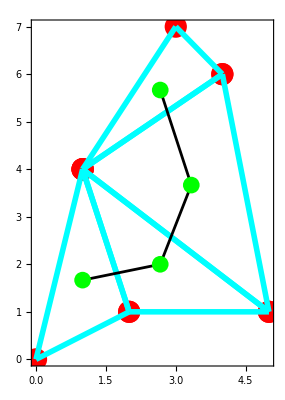

Graph of a set of simplices in 3D
:

-Graphics3D-

```mathematica
If [ testmode==1,
pointsize=0.04; 
pointcolor={1,0,0};
thickness=0.01;
linecolor={0,1,1};
pointsize1=0.03;
pointcolor1={0,1,0};
thickness1=0.005;
linecolor1={0,0,0};
points2d1={{0,0},{1,4},{2,1},{5,1},{4,6},{3,7}};simp2d1={{points2d1⟦1⟧,points2d1⟦2⟧,points2d1⟦3⟧},{points2d1⟦2⟧,points2d1⟦3⟧,points2d1⟦4⟧},{points2d1⟦2⟧,points2d1⟦4⟧,points2d1⟦5⟧},{points2d1⟦2⟧,points2d1⟦5⟧,points2d1⟦6⟧}};
simp2dcent=simplexcenters[simp2d1];

points3d1={{0,0,0},{1,4,0},{2,1,0},{1,2,3},{1,1,-1}};simp3d1={{points3d1⟦1⟧,points3d1⟦2⟧,points3d1⟦3⟧,points3d1⟦4⟧},
{points3d1⟦1⟧,points3d1⟦2⟧,points3d1⟦3⟧,points3d1⟦5⟧}};
simp3dcent=simplexcenters[simp3d1];

grsimp2d=simplexgraph[simp2d1,pointsize,thickness,pointcolor,linecolor];grsimpcent2d=pointsgraph[simp2dcent,pointsize1,thickness1,pointcolor1,Null];

grsimp3d=simplexgraph[simp3d1,pointsize,thickness,pointcolor,linecolor];
grsimpcent3d=pointsgraph[simp3dcent,pointsize1,thickness1,pointcolor1,Null];

];

If [testmode≠0,
Print["Graph of a set of simplices in 2D: \n"];
Show[grsimp2d,grsimpcent2d,PlotRange->All,Frame->True]
]
If [testmode≠0,
Print["\nGraph of a set of simplices in 3D\n:"];
Show[grsimp3d,grsimpcent3d
,PlotRange->All
,Axes->True
,FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}}
,AxesLabel->{"x","y","z  "}
,BoxRatios->{1,1,1}
,PlotRange->All
,ViewPoint->{3.892, -7.185, 3.771}]
]
```

# Additional utilities (unfinished or seldomly used)

## Data exchange through files

Format conversion for Input/output of data structures via strings

### Function outputform for outputting expressions to files or for sending them to C programs for parsing:

```mathematica
outputform[expr_]:=ToString[outputform1[expr]];

outputform1[expr_]:=Module[{i},
(* $A Igor mar06; *)

If[Depth[expr]==1,
Return[CForm[expr]]
];
Table[outputform1[ expr[[i]] ],{i,1,Length[expr]}]
];
```

### Function strmathform changes the numbers in e notation (e.g. 1.2e-10) to the Mathematica form (e.g. 1.2*10^-10) in a text string:

```mathematica
strmathform[strarg_]:=Module[{positions,str,i,pos,ch1,ch2},
(* $A Igor apr06; *)

str=strarg;
(* find potential exponents in e- notation for real numbers: *)
positions=StringPosition[str,{"e","E"}];
positions=Transpose[Reverse[positions]][[1]];
(*
Print["strmathform: str= <",str,">, exp. positions: ",positions];
*)
(* Eliminate those positions that do not belong to e-notations: *)
For[i=Length[positions],i≥1,i=i-1,
pos=positions[[i]];
If[pos>1,
ch1=StringTake[str,{pos-1,pos-1}],
ch1="!";  (* this will eliminate the current position *)
];
If[pos<StringLength[str],
ch2=StringTake[str,{pos+1,pos+1}],
ch2="!";   (* this will eliminate the current position *)
];

(*
Print["Deciding on elimination of position ",i," (",positions[[i]],"), ch1= ",ch1,", ch2= ",ch2];
*)

If[ (ch1!="." &&  ¬DigitQ[ch1] || ch2≠"+" && ch2!="-" && ¬DigitQ[ch2]),
positions=Delete[positions,i];
];
];

(*
Print["Exp. positions after elimination of false positions: ",positions];
*)

If[Length[positions]>0,

(*
str=StringReplacePart[str,"*10^",
Table[{positions[[i]],positions[[i]]},{i,1,Length[positions]}
];
];
*)

str=StringReplacePart[str,"*10^",
Table[{positions[[i]],positions[[i]]},{i,1,Length[positions]}
]
]

];
Return[str];
];
```

### Tests

#### strmathform

```mathematica
If[testmode≠0,
str="{1.2e-10, 15, 1e-20, \"teac\",1/3e25}"
,,]
```

```mathematica
If[testmode≠0,
mathstr=strmathform[str]
,,]
```

```mathematica
If[testmode≠0,
expr=ToExpression[mathstr]
,,]
```

```mathematica
If[testmode≠0,
FullForm[ expr[[4]] ]
,,]
```

#### outputform

```mathematica
If[testmode≠0,
expr={25,1/3,{1.2*10^-10, 15,1/10}, 1*10^-20, "teac"}
,,]
```

```mathematica
If[testmode≠0,
outputform[expr]
,,]
```

```mathematica
If[testmode≠0,
outputform[N[expr]]
,,]
```

#### Whole export/import cycle

```mathematica
If[testmode≠0,
(*
form="Lines";
form="Table";
form="List";
form="CSV";
*)
form="Text";

expr={{ {1.1,1.2},{2.1,2.2,2.3},3 } ,10^-16,5.5*10^22,"xy",bcd}
,,]
```

```mathematica
If[testmode≠0,
outstr= outputform[expr]
,,]
```

```mathematica
If[testmode≠0,
instr=ImportString[outstr,"Text"]
,,]
```

```mathematica
If[testmode≠0,
{Head[impstr],Length[impstr]}
,,]
```

```mathematica
If[testmode≠0,
expr1=ToExpression[strmathform[impstr]]
,,]
```

```mathematica
If[testmode≠0,
expr==expr1
,,]
```

```mathematica
If[testmode≠0,
CharacterRange["C","f"]
,,]
```

Output to files for reading in C

### Output & input of tables: - development stage

#### exporttable [ filename, tab ] importtable [ filename ] exporttable writes 1D or 2D table tab to file named filename (existing files are overwritten), numbers are separated by commas (lines of matrices by new lines), numbers are written in E notation. importtable imports a table in this format from the file names filename.

```mathematica
exporttable[filename_,tab_]:=Export[filename,N[tab],"CSV"];
importtable[filename_]:=Import[filename,"CSV"];
```

#### Test of exporting/importing a table:

2d table, 3x2

```mathematica
If[testmode≠0,
tab={{1.1,1.2},{2.1,2.2},{1/3,4.55*10^-26}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

2d table, different lengths of lines

```mathematica
If[testmode≠0,
tab={{1.1,1.2,1.3,1.4},{2.1,2.2},{1/3,4.55*10^-26},{5.5}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

1d table, different lengths of lines

```mathematica
If[testmode≠0,
tab={1,2,3,4,1/3,4.55*10^-26,5.5}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

```mathematica
If[testmode≠0,
Flatten[tab1]==tab
,,]
```

Deeper Tables

```mathematica
If[testmode≠0,
tab={{1.1,1.2},{2.1,2.2,{2.31,2.32},2.4},{3.1,3.2}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

```mathematica
If[testmode≠0,
tab1[[2,3]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[tab1[[2,3]]]
,,]
```

#### Experimentation for outputting tables (for development stage)

Write a table & check file contents -   Save

```mathematica
If[testmode≠0,
table={{1.1,1.2},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
Save["test.out",table];

Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

Write a table & check file contents -   Put

```mathematica
If[testmode≠0,
table={{1.1,1.2},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
table1={1,2}
,,]
```

```mathematica
If[testmode≠0,
Put[table1,table,"test.out"];
,,]


If[testmode≠0,
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

Write a table & check file contents -   Export

```mathematica
If[testmode≠0,
table={{1.1,1.2,111,222,{3,4}},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
table1={1,2}
,,]
```

```mathematica
If[testmode≠0,

tablenum=N[table]
,,]
```

```mathematica
If[testmode≠0,

form="Text";
form="List";
form="Lines";
form="Table";
form="CSV";

Export["test.out",table,form];

Import["test.out","Text"]  (* Show contents of the file *)

,,]
```

```mathematica
If[testmode≠0,

Export["test.out",tablenum,form];

Import["test.out","Text"]  (* Show contents of the file *)

,,]
```

```mathematica
If[testmode≠0,
tabin=Import["test.out","CSV"]
,,]
```

```mathematica
If[testmode≠0,
FullForm[tabin]
,,]
```

### Storing data for retrieval in Mathematica

#### This demonstrate how data from Mathematica can be stored in files such that it is easily read in another mathematica sessions.

```mathematica
(*
SetDirectory["C:/users/igor/doc/pr/enlub/work/SRT_identification_2006-01-20/StripReduction/"
];
*)
Directory[]
```

C:\Program Files\Wolfram Research\Mathematica\5.2

```mathematica
expr1={1.0,{2.1,2.3,{2.41}},3.1,1/3,"Text",6.02*10^-23,1/1000};
expr2={1,2,3};

expr1
```

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

#### Writing expressions (& values) in standard form to a file: Warning: number notation is in Mathematica form. To convert to C form, import expression to Mathematica (assign to a variable), convert to suitable string form, and write back to a file. Note: Use of N[] for converting to approximate decimal numbers is not necessary since numbers will anyway be in Mathematica format

```mathematica
(* Write standard representation of expr1 to test.out, overwrite file *)
expr1>>"test.out";  
(* Append standard representation of expr1 to file test.out: *)
N[expr2]>>>"test.out" ;
!!"test.out"
```

{1., {2.1, 2.3, {2.41}}, 3.1, 1/3, "Text", 6.02*^-23, 1/1000}
{1., 2., 3.}

Use stdout for cell output:

```mathematica
(* Write standard representation of expr1 to test.out, overwrite file *)
expr1>>"stdout";  
(* Append standard representation of expr1 to file test.out: *)
expr2>>"stdout"
```

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

{1,2,3}

#### Saving definitions of variable or function definitions in standard form in a file: Warning: Number notation is in Mathematica form. To convert to C form, import expression to Mathematica (assign to a variable), convert to suitable string form, and write back to a file. Notes Save appends to a file. For restoring definitions, simply read in the file by using << "filename"

```mathematica
"Definitions:">>test.out;  (* clears contents of the file *)
Save["test.out",{expr1,expr2}];
```

```mathematica
!!"test.out"
```

"Definitions:"
expr1 = {1., {2.1, 2.3, {2.41}}, 3.1, 1/3, "Text", 6.02*^-23, 1/1000}
 
expr2 = {1, 2, 3}

#### Restoring variable and function definitions saved to a file:

```mathematica
expr1={};
expr2={};
expr1
expr2
<< "test.out" ;
expr1
expr2
```

{}

{}

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

{1,2,3}

#### Export from Mathematica:

```mathematica
exprvalue={{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,10^-16,5.5*10^22,"xy"}
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,5.5×10^22,xy}

```mathematica
N[exprvalue]
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1.×10^-16,5.5×10^22,xy}

```mathematica
CForm[exprvalue]  /.  List(x_)->{x}
```

List(List(List(1.1,1.2),List(2.1,2.2,2.3),3.),1.e-16,5.5e22,"xy")

#### Import to Mathematica:

```mathematica
exprstr="{{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,1e-16,\"xy\"}"
```

{{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,1e-16,"xy"}

```mathematica
exprstr="{1e-22}"
```

{1e-22}

ToExpression ne dela v redu:

```mathematica
expr=ToExpression[exprstr,InputForm]
```

{-22+e}

```mathematica
form="List";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{1e-22}}

```mathematica
expr[[0]]
```

List

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1e-22},String}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1e-22},String}

```mathematica
form="Table";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{{1e-22}}}

```mathematica
expr[[0]]
```

List

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{{1e-22}},List}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{{1e-22}},List}

```mathematica
form="Lines";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{1e-22}}

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1e-22},String}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1e-22},String}

```mathematica
exprstr="1.22e-25"
```

1.22e-25

```mathematica
form="CSV";
expr=ImportString[exprstr,form]
```

{{1.22×10^-25}}

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1.22×10^-25},List}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1.22×10^-25},List}

```mathematica
{expr[[1,1]],expr[[1,1,0]]}
```

{1.22×10^-25,Real}

```mathematica
{expr[[-1,1]],expr[[-1,1,0]]}
```

{1.22×10^-25,Real}

```mathematica
FullForm[expr]
```

List[List[1.22×10^-25]]

#### Export/Import strings:

```mathematica
exprvalue={{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,10^-16,"xy"}
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}

```mathematica
form="Lines";
{exprstr=ExportString[exprvalue,form,ConversionOptions->{"ListSeparators"->{","}}],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.},1/10000000000000000,xy},  Check: ,{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}=={{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}}

```mathematica
form="List";
{exprstr=ExportString[exprvalue,form,ConversionOptions->{"ListSeparators"->{","}}],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "1.2},". More…
                                                   ^

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "2.2, ". More…
                                                   ^

ToExpression::sntx: Syntax error in or before "2.3},". More…
                                                   ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation. More…

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{1.1,,1.2},,{2.1,,2.2,,2.3},,3.},1/10000000000000000,xy},  Check: ,False}

```mathematica
form="CSV";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}"
1/10000000000000000
xy,""{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}"
1/10000000000000000
xy",{{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Table";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "1.2},". More…
                                                   ^

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "2.2, ". More…
                                                   ^

ToExpression::sntx: Syntax error in or before "2.3},". More…
                                                   ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation. More…

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{{1.1,,1.2},,{2.1,,2.2,,2.3},,3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Text";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

ToExpression::sntx: 
   Syntax error in or before 
    "{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                                           ^
     ". More…

{                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000,"                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000",                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000,  Check: ,$Failed=={{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}}

```mathematica
form="TSV";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Words";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{1.1
1.2
2.1
2.2
2.299999999999999
3.
1/10000000000000000
xy,"1.1
1.2
2.1
2.2
2.299999999999999
3.
1/10000000000000000
xy",{1.1,1.2,2.1,2.2,2.299999999999999,3.,1/10000000000000000,xy},  Check: ,False}